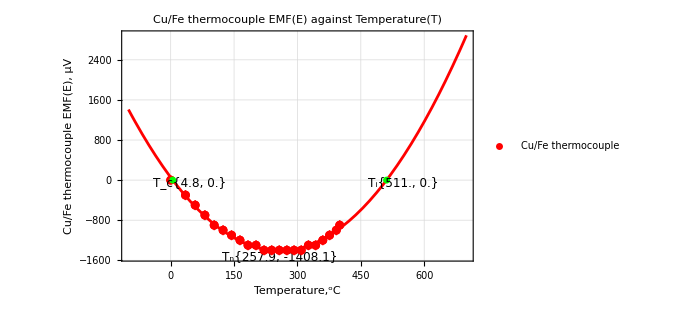

```mathematica
(*graph before shifted*)
(*Data and Error Definitions*)t1={{0,0},{35,-300},{58,-500},{81,-700},{103,-900},{124,-1000},{144,-1100},{164,-1200},{183,-1300},{202,-1300},{221,-1400},{239,-1400},{257,-1400},{275,-1400},{292,-1400},{309,-1400},{326,-1300},{343,-1300},{360,-1200},{376,-1100},{392,-1000},{400,-900}};

(*Define the error bar*)
t1error={{Around[0,0],Around[0,0]},
{Around[35,0.5],Around[-300,100]},
{Around[58,0.5],Around[-500,100]},
{Around[81,0.5],Around[-700,100]},
{Around[103,0.5],Around[-900,100]},
{Around[124,0.5],Around[-1000,100]},
{Around[144,0.5],Around[-1100,100]},
{Around[164,0.5],Around[-1200,100]},
{Around[183,0.5],Around[-1300,100]},
{Around[202,0.5],Around[-1300,100]},
{Around[221,0.5],Around[-1400,100]},
{Around[239,0.5],Around[-1400,100]},
{Around[257,0.5],Around[-1400,100]},
{Around[275,0.5],Around[-1400,100]},
{Around[292,0.5],Around[-1400,100]},
{Around[309,0.5],Around[-1400,100]},
{Around[326,0.5],Around[-1300,100]},
{Around[343,0.5],Around[-1300,100]},
{Around[360,0.5],Around[-1200,100]},
{Around[376,0.5],Around[-1100,100]},
{Around[392,0.5],Around[-1000,100]},
{Around[400,0.5],Around[-900,100]}};


(*Curve Fitting*)
x1=t1[[All,1]];
y1=t1[[All,2]];
fit1=Fit[Transpose[{x1,y1}],{1,x,x^2},x];

(*Finding Intersection Points with Y=0 Line*)
solutions=NSolve[fit1==0,x];
intersectionPoints={#,0}&/@(x/. solutions);

(*Finding the Minimum Point*)
minX=x/. Last[FindMinimum[fit1,{x,0}]];
minY=fit1/. x->minX;
minPoint={minX,minY};

(*Labeling Function*)
labelPoint[pt_,label_,offset_]:=Text[Style[label<>ToString[Round[pt,0.1]],Black,12],pt+offset]

(*Plotting*)
Show[ListPlot[{t1},PlotStyle->{Red}],ListPlot[{t1error},PlotStyle->{Red},PlotLegends->{"Cu/Fe thermocouple"}],Plot[{fit1},{x,-100,700},PlotStyle->{Red}],Graphics[{Blue,PointSize[0.01],Point[minPoint],labelPoint[minPoint,"T_n",{0,-120}]}],Graphics[{Green,PointSize[0.01],Point[intersectionPoints],labelPoint[intersectionPoints[[1]],"T_c",{40,-50}],labelPoint[intersectionPoints[[2]],"T_i",{40,-50}]}],Frame->True,FrameLabel->{"Temperature,^oC","Cu/Fe thermocouple EMF(E), µV"},GridLines->Automatic,PlotLabel->"Cu/Fe thermocouple EMF(E) against Temperature(T)",ImageSize->500,PlotRange->{{-50,580},{200,-1500}}]
```

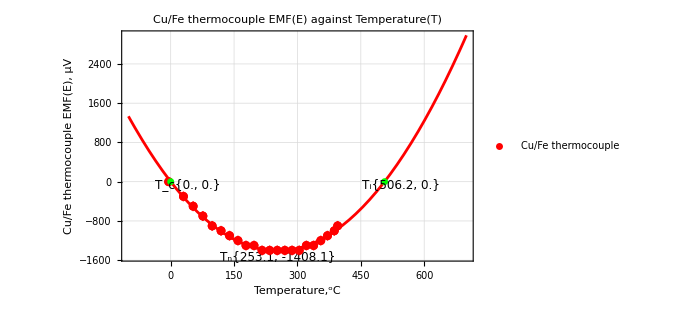

```mathematica
(*graph after shif*)
(*Data and Error Definitions with Shift*)t1={{0-4.8,0},{35-4.8,-300},{58-4.8,-500},{81-4.8,-700},{103-4.8,-900},{124-4.8,-1000},{144-4.8,-1100},{164-4.8,-1200},{183-4.8,-1300},{202-4.8,-1300},{221-4.8,-1400},{239-4.8,-1400},{257-4.8,-1400},{275-4.8,-1400},{292-4.8,-1400},{309-4.8,-1400},{326-4.8,-1300},{343-4.8,-1300},{360-4.8,-1200},{376-4.8,-1100},{392-4.8,-1000},{400-4.8,-900}};

(*Adjust t1error by Subtracting 4.8 from Each x-value*)t1error={{Around[0-4.8,0],Around[0,0]},{Around[35-4.8,0.5],Around[-300,100]},{Around[58-4.8,0.5],Around[-500,100]},{Around[81-4.8,0.5],Around[-700,100]},{Around[103-4.8,0.5],Around[-900,100]},{Around[124-4.8,0.5],Around[-1000,100]},{Around[144-4.8,0.5],Around[-1100,100]},{Around[164-4.8,0.5],Around[-1200,100]},{Around[183-4.8,0.5],Around[-1300,100]},{Around[202-4.8,0.5],Around[-1300,100]},{Around[221-4.8,0.5],Around[-1400,100]},{Around[239-4.8,0.5],Around[-1400,100]},{Around[257-4.8,0.5],Around[-1400,100]},{Around[275-4.8,0.5],Around[-1400,100]},{Around[292-4.8,0.5],Around[-1400,100]},{Around[309-4.8,0.5],Around[-1400,100]},{Around[326-4.8,0.5],Around[-1300,100]},{Around[343-4.8,0.5],Around[-1300,100]},{Around[360-4.8,0.5],Around[-1200,100]},{Around[376-4.8,0.5],Around[-1100,100]},{Around[392-4.8,0.5],Around[-1000,100]},{Around[400-4.8,0.5],Around[-900,100]}};

(*Curve Fitting*)
x1=t1[[All,1]];
y1=t1[[All,2]];
fit1=Fit[Transpose[{x1,y1}],{1,x,x^2},x];

(*Finding Intersection Points with Y=0 Line*)
solutions=NSolve[fit1==0,x];
intersectionPoints={#,0}&/@(x/. solutions);

(*Finding the Minimum Point*)
minX=x/. Last[FindMinimum[fit1,{x,0}]];
minY=fit1/. x->minX;
minPoint={minX,minY};

(*Labeling Function*)
labelPoint[pt_,label_,offset_]:=Text[Style[label<>ToString[Round[pt,0.1]],Black,12],pt+offset]

(*Plotting*)
Show[ListPlot[{t1},PlotStyle->{Red}],ListPlot[{t1error},PlotStyle->{Red},PlotLegends->{"Cu/Fe thermocouple"}],Plot[{fit1},{x,-100,700},PlotStyle->{Red}],Graphics[{Blue,PointSize[0.01],Point[minPoint],labelPoint[minPoint,"T_n",{0,-120}]}],Graphics[{Green,PointSize[0.01],Point[intersectionPoints],labelPoint[intersectionPoints[[1]],"T_c",{40,-50}],labelPoint[intersectionPoints[[2]],"T_i",{40,-50}]}],Frame->True,FrameLabel->{"Temperature,^oC","Cu/Fe thermocouple EMF(E), µV"},GridLines->Automatic,PlotLabel->"Cu/Fe thermocouple EMF(E) against Temperature(T)",ImageSize->500,PlotRange->{{-50,580},{200,-1500}}]
```

```mathematica
(*coordinate of point*)
(*Data and Error Definitions with Shift*)t1={{0-4.8,0},{35-4.8,-300},{58-4.8,-500},{81-4.8,-700},{103-4.8,-900},{124-4.8,-1000},{144-4.8,-1100},{164-4.8,-1200},{183-4.8,-1300},{202-4.8,-1300},{221-4.8,-1400},{239-4.8,-1400},{257-4.8,-1400},{275-4.8,-1400},{292-4.8,-1400},{309-4.8,-1400},{326-4.8,-1300},{343-4.8,-1300},{360-4.8,-1200},{376-4.8,-1100},{392-4.8,-1000},{400-4.8,-900}};

(*Adjust t1error by Subtracting 4.8 from Each x-value*)t1error={{Around[0-4.8,0],Around[0,0]},{Around[35-4.8,0.5],Around[-300,100]},{Around[58-4.8,0.5],Around[-500,100]},{Around[81-4.8,0.5],Around[-700,100]},{Around[103-4.8,0.5],Around[-900,100]},{Around[124-4.8,0.5],Around[-1000,100]},{Around[144-4.8,0.5],Around[-1100,100]},{Around[164-4.8,0.5],Around[-1200,100]},{Around[183-4.8,0.5],Around[-1300,100]},{Around[202-4.8,0.5],Around[-1300,100]},{Around[221-4.8,0.5],Around[-1400,100]},{Around[239-4.8,0.5],Around[-1400,100]},{Around[257-4.8,0.5],Around[-1400,100]},{Around[275-4.8,0.5],Around[-1400,100]},{Around[292-4.8,0.5],Around[-1400,100]},{Around[309-4.8,0.5],Around[-1400,100]},{Around[326-4.8,0.5],Around[-1300,100]},{Around[343-4.8,0.5],Around[-1300,100]},{Around[360-4.8,0.5],Around[-1200,100]},{Around[376-4.8,0.5],Around[-1100,100]},{Around[392-4.8,0.5],Around[-1000,100]},{Around[400-4.8,0.5],Around[-900,100]}};

(*Curve Fitting*)
x1=t1[[All,1]];
y1=t1[[All,2]];
fit1=Fit[Transpose[{x1,y1}],{1,x,x^2},x];

(*Finding Intersection Points with Y=0 Line*)
solutions=NSolve[fit1==0,x];
intersectionPoints={#,0}&/@(x/. solutions);

(*Finding the Minimum Point*)
minX=x/. Last[FindMinimum[fit1,{x,0}]];
minY=fit1/. x->minX;
minPoint={minX,minY};

(*Labeling Function*)
labelPoint[pt_,label_,offset_]:=Text[Style[label<>ToString[Round[pt,0.1]],Black,12],pt+offset]

(*Evaluate the fitted curve at specific x-values*)xValuesToList={25,50,75,100,125,150,175,200,225,250,275,300,325,350,375,400,425}; (*example x-values*)
pointsOnCurve={#,fit1/. x->#}&/@xValuesToList;

(*Creating a list of coordinates*)coordinateList=Table[{"Point at x = ",xValuesToList[[i]],": ",pointsOnCurve[[i]]},{i,1,Length[pointsOnCurve]}];

(*Plotting with Coordinate List Below the Graph*)plot=Show[ListPlot[{t1},PlotStyle->{Red}],ListPlot[{t1error},PlotStyle->{Red},PlotLegends->{"Cu/Fe thermocouple"}],Plot[{fit1},{x,-100,700},PlotStyle->{Red}],Graphics[{Blue,PointSize[0.01],Point[minPoint],labelPoint[minPoint,"\!\(\*SubscriptBox[\(T\), \(n\)]\)",{0,-120}]}],Graphics[{Green,PointSize[0.01],Point[intersectionPoints],labelPoint[intersectionPoints[[1]],"\!\(\*SubscriptBox[\(T\), \(c\)]\)",{40,-50}],labelPoint[intersectionPoints[[2]],"\!\(\*SubscriptBox[\(T\), \(i\)]\)",{40,-50}]}],Frame->True,FrameLabel->{"Temperature,\!\(\*SuperscriptBox[\(\\\ \), \(o\)]\)C","Cu/Fe thermocouple EMF(E), µV"},GridLines->Automatic,PlotLabel->"Cu/Fe thermocouple EMF(E) against Temperature(T)",ImageSize->500,PlotRange->{{-50,580},{200,-1500}}];

(*Arranging Plot and Coordinates Vertically*)
Column[{plot,Grid[coordinateList,Alignment->Left]}]
```

-Graphics-
Point at x =  | 25 | :  | {25,-264.012}
Point at x =  | 50 | :  | {50,-501.046}
Point at x =  | 75 | :  | {75,-710.596}
Point at x =  | 100 | :  | {100,-892.663}
Point at x =  | 125 | :  | {125,-1047.25}
Point at x =  | 150 | :  | {150,-1174.34}
Point at x =  | 175 | :  | {175,-1273.96}
Point at x =  | 200 | :  | {200,-1346.09}
Point at x =  | 225 | :  | {225,-1390.74}
Point at x =  | 250 | :  | {250,-1407.9}
Point at x =  | 275 | :  | {275,-1397.58}
Point at x =  | 300 | :  | {300,-1359.78}
Point at x =  | 325 | :  | {325,-1294.49}
Point at x =  | 350 | :  | {350,-1201.71}
Point at x =  | 375 | :  | {375,-1081.46}
Point at x =  | 400 | :  | {400,-933.719}
Point at x =  | 425 | :  | {425,-758.496}

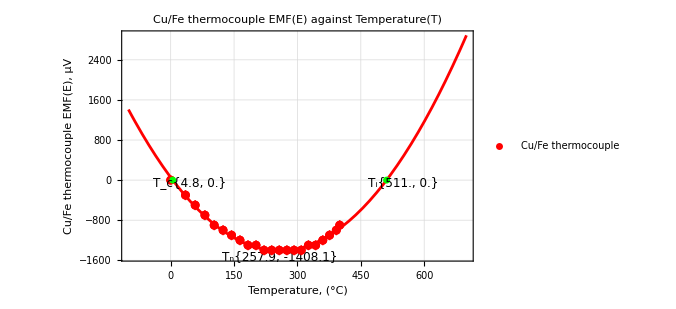
-Graphics-
Gradients at Specific Points:
{Gradient at x = 25: -10.2421,Gradient at x = 50: -9.14276,Gradient at x = 75: -8.04341,Gradient at x = 100: -6.94405,Gradient at x = 125: -5.8447,Gradient at x = 150: -4.74535,Gradient at x = 175: -3.64599,Gradient at x = 200: -2.54664,Gradient at x = 225: -1.44729,Gradient at x = 250: -0.347932,Gradient at x = 275: 0.751422,Gradient at x = 300: 1.85078,Gradient at x = 325: 2.95013,Gradient at x = 350: 4.04948,Gradient at x = 375: 5.14884,Gradient at x = 400: 6.24819}

```mathematica
(*finding the gradient of certain points*)
(*Data and Error Definitions*)t1={{0,0},{35,-300},{58,-500},{81,-700},{103,-900},{124,-1000},{144,-1100},{164,-1200},{183,-1300},{202,-1300},{221,-1400},{239,-1400},{257,-1400},{275,-1400},{292,-1400},{309,-1400},{326,-1300},{343,-1300},{360,-1200},{376,-1100},{392,-1000},{400,-900}};

(*Define the error bar*)
t1error={{Around[0,0],Around[0,0]},
{Around[35,0.5],Around[-300,100]},
{Around[58,0.5],Around[-500,100]},
{Around[81,0.5],Around[-700,100]},
{Around[103,0.5],Around[-900,100]},
{Around[124,0.5],Around[-1000,100]},
{Around[144,0.5],Around[-1100,100]},
{Around[164,0.5],Around[-1200,100]},
{Around[183,0.5],Around[-1300,100]},
{Around[202,0.5],Around[-1300,100]},
{Around[221,0.5],Around[-1400,100]},
{Around[239,0.5],Around[-1400,100]},
{Around[257,0.5],Around[-1400,100]},
{Around[275,0.5],Around[-1400,100]},
{Around[292,0.5],Around[-1400,100]},
{Around[309,0.5],Around[-1400,100]},
{Around[326,0.5],Around[-1300,100]},
{Around[343,0.5],Around[-1300,100]},
{Around[360,0.5],Around[-1200,100]},
{Around[376,0.5],Around[-1100,100]},
{Around[392,0.5],Around[-1000,100]},
{Around[400,0.5],Around[-900,100]}};

(*Curve Fitting*)
x1=t1[[All,1]];
y1=t1[[All,2]];
fit1=Fit[Transpose[{x1,y1}],{1,x,x^2},x];

(*Finding the Derivative*)
derivative=D[fit1,x];

(*Define a list of specific x values where you want to find the gradient*)
specificXValues={25,50,75,100,125,150,175,200,225,250,275,300,325,350,375,400};  (*Replace with your desired x values*)

(*Calculating the Gradient at the Specific Points*)
gradientAtSpecificPoints=Table[{xVal,derivative/. x->xVal},{xVal,specificXValues}];

(*Finding Intersection Points with Y=0 Line*)
solutions=NSolve[fit1==0,x];
intersectionPoints={#,0}&/@(x/. solutions);

(*Finding the Minimum Point*)
minX=x/. Last[FindMinimum[fit1,{x,0}]];
minY=fit1/. x->minX;
minPoint={minX,minY};

(*Labeling Function*)
labelPoint[pt_,label_,offset_]:=Text[Style[label<>ToString[Round[pt,0.1]],Black,12],pt+offset]

(*Plotting*)
plot=Show[ListPlot[{t1},PlotStyle->{Red}],ListPlot[{t1error},PlotStyle->{Red},PlotLegends->{"Cu/Fe thermocouple"}],Plot[{fit1},{x,-100,700},PlotStyle->{Red}],Graphics[{Blue,PointSize[0.01],Point[minPoint],labelPoint[minPoint,"T_n",{0,-120}]}],Graphics[{Green,PointSize[0.01],Point[intersectionPoints],labelPoint[intersectionPoints[[1]],"T_c",{40,-50}],labelPoint[intersectionPoints[[2]],"T_i",{40,-50}]}],Frame->True,FrameLabel->{"Temperature, (°C)","Cu/Fe thermocouple EMF(E), µV"},GridLines->Automatic,PlotLabel->"Cu/Fe thermocouple EMF(E) against Temperature(T)",ImageSize->500,PlotRange->{{-50,580},{200,-1500}}];

(*Gradient Display*)
gradientDisplay=Table["Gradient at x = "<>ToString[point[[1]]]<>": "<>ToString[point[[2]]],{point,gradientAtSpecificPoints}];

(*Combine Plot and Gradient Display*)
Column[{plot,"Gradients at Specific Points:",gradientDisplay}]
```

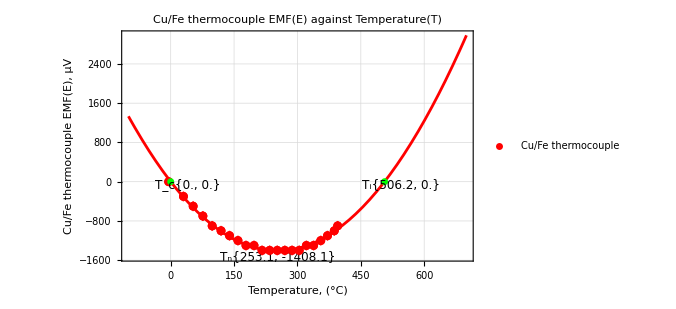
-Graphics-
Points on Curve:
Point at x =  | 25 | :  | {25,-264.012}
Point at x =  | 50 | :  | {50,-501.046}
Point at x =  | 75 | :  | {75,-710.596}
Point at x =  | 100 | :  | {100,-892.663}
Point at x =  | 125 | :  | {125,-1047.25}
Point at x =  | 150 | :  | {150,-1174.34}
Point at x =  | 175 | :  | {175,-1273.96}
Point at x =  | 200 | :  | {200,-1346.09}
Point at x =  | 225 | :  | {225,-1390.74}
Point at x =  | 250 | :  | {250,-1407.9}
Point at x =  | 275 | :  | {275,-1397.58}
Point at x =  | 300 | :  | {300,-1359.78}
Point at x =  | 325 | :  | {325,-1294.49}
Point at x =  | 350 | :  | {350,-1201.71}
Point at x =  | 375 | :  | {375,-1081.46}
Point at x =  | 400 | :  | {400,-933.719}
Point at x =  | 425 | :  | {425,-758.496}
Gradients at Specific Points:
Gradient at x =  | 25 | :  | -10.031
Gradient at x =  | 50 | :  | -8.93168
Gradient at x =  | 75 | :  | -7.83233
Gradient at x =  | 100 | :  | -6.73298
Gradient at x =  | 125 | :  | -5.63362
Gradient at x =  | 150 | :  | -4.53427
Gradient at x =  | 175 | :  | -3.43492
Gradient at x =  | 200 | :  | -2.33556
Gradient at x =  | 225 | :  | -1.23621
Gradient at x =  | 250 | :  | -0.136856
Gradient at x =  | 275 | :  | 0.962498
Gradient at x =  | 300 | :  | 2.06185
Gradient at x =  | 325 | :  | 3.1612
Gradient at x =  | 350 | :  | 4.26056
Gradient at x =  | 375 | :  | 5.35991
Gradient at x =  | 400 | :  | 6.45927

```mathematica
(*Data and Error Definitions with Shift*)t1={{0-4.8,0},{35-4.8,-300},{58-4.8,-500},{81-4.8,-700},{103-4.8,-900},{124-4.8,-1000},{144-4.8,-1100},{164-4.8,-1200},{183-4.8,-1300},{202-4.8,-1300},{221-4.8,-1400},{239-4.8,-1400},{257-4.8,-1400},{275-4.8,-1400},{292-4.8,-1400},{309-4.8,-1400},{326-4.8,-1300},{343-4.8,-1300},{360-4.8,-1200},{376-4.8,-1100},{392-4.8,-1000},{400-4.8,-900}};

(*Adjust t1error by Subtracting 4.8 from Each x-value*)t1error={{Around[0-4.8,0],Around[0,0]},{Around[35-4.8,0.5],Around[-300,100]},{Around[58-4.8,0.5],Around[-500,100]},{Around[81-4.8,0.5],Around[-700,100]},{Around[103-4.8,0.5],Around[-900,100]},{Around[124-4.8,0.5],Around[-1000,100]},{Around[144-4.8,0.5],Around[-1100,100]},{Around[164-4.8,0.5],Around[-1200,100]},{Around[183-4.8,0.5],Around[-1300,100]},{Around[202-4.8,0.5],Around[-1300,100]},{Around[221-4.8,0.5],Around[-1400,100]},{Around[239-4.8,0.5],Around[-1400,100]},{Around[257-4.8,0.5],Around[-1400,100]},{Around[275-4.8,0.5],Around[-1400,100]},{Around[292-4.8,0.5],Around[-1400,100]},{Around[309-4.8,0.5],Around[-1400,100]},{Around[326-4.8,0.5],Around[-1300,100]},{Around[343-4.8,0.5],Around[-1300,100]},{Around[360-4.8,0.5],Around[-1200,100]},{Around[376-4.8,0.5],Around[-1100,100]},{Around[392-4.8,0.5],Around[-1000,100]},{Around[400-4.8,0.5],Around[-900,100]}};

(*Curve Fitting*)
x1=t1[[All,1]];
y1=t1[[All,2]];
fit1=Fit[Transpose[{x1,y1}],{1,x,x^2},x];

(*Finding the Derivative*)
derivative=D[fit1,x];

(*Define a list of specific x values where you want to find the gradient*)
specificXValues={25,50,75,100,125,150,175,200,225,250,275,300,325,350,375,400};  (*Replace with your desired x values*)

(*Calculating the Gradient at the Specific Points*)
gradientAtSpecificPoints=Table[{xVal,derivative/. x->xVal},{xVal,specificXValues}];

(*Finding Intersection Points with Y=0 Line*)
solutions=NSolve[fit1==0,x];
intersectionPoints={#,0}&/@(x/. solutions);

(*Finding the Minimum Point*)
minX=x/. Last[FindMinimum[fit1,{x,0}]];
minY=fit1/. x->minX;
minPoint={minX,minY};

(*Labeling Function*)
labelPoint[pt_,label_,offset_]:=Text[Style[label<>ToString[Round[pt,0.1]],Black,12],pt+offset]

(*Evaluate the fitted curve at specific x-values*)xValuesToList={25,50,75,100,125,150,175,200,225,250,275,300,325,350,375,400,425}; (*example x-values*)
pointsOnCurve={#,fit1/. x->#}&/@xValuesToList;

(*Creating a list of coordinates*)coordinateList=Table[{"Point at x = ",xValuesToList[[i]],": ",pointsOnCurve[[i]]},{i,1,Length[pointsOnCurve]}];

(*Plotting*)
plot=Show[ListPlot[{t1},PlotStyle->{Red}],ListPlot[{t1error},PlotStyle->{Red},PlotLegends->{"Cu/Fe thermocouple"}],Plot[{fit1},{x,-100,700},PlotStyle->{Red}],Graphics[{Blue,PointSize[0.01],Point[minPoint],labelPoint[minPoint,"T_n",{0,-120}]}],Graphics[{Green,PointSize[0.01],Point[intersectionPoints],labelPoint[intersectionPoints[[1]],"T_c",{40,-50}],labelPoint[intersectionPoints[[2]],"T_i",{40,-50}]}],Frame->True,FrameLabel->{"Temperature, (°C)","Cu/Fe thermocouple EMF(E), µV"},GridLines->Automatic,PlotLabel->"Cu/Fe thermocouple EMF(E) against Temperature(T)",ImageSize->500,PlotRange->{{-50,580},{200,-1500}}];

(*Create a formatted grid for gradients*)gradientList=Table[{"Gradient at x = ",xValuesToList[[i]],": ",gradientAtSpecificPoints[[i,2]]},{i,1,Length[gradientAtSpecificPoints]}];

(*Combine coordinateList and gradientList for display,formatted as a grid*)
combinedDisplay=Column[{plot,"Points on Curve:",Grid[coordinateList,Alignment->Left,Frame->False],"Gradients at Specific Points:",Grid[gradientList,Alignment->Left,Frame->False] (*Format as a grid with a frame for clarity*)}]
```